```mathematica
hpt = Abs@Import["hPeriod", "Table", Path->NotebookDirectory[]];
hPeriod = hpt[[All,1]] / hpt[[All,2]];
hpmt = Abs@Import["hPeriodMultiples", "Table", Path->NotebookDirectory[]];
hPeriodMultiple = hpmt[[All,1]] / hpmt[[All,2]];
vpt = Abs@Import["vPeriod", "Table", Path->NotebookDirectory[]];
vPeriod = vpt[[All,1]] / vpt[[All,2]];
vpmt = Abs@Import["vPeriodMultiples", "Table", Path->NotebookDirectory[]];
vPeriodMultiple = vpmt[[All,1]] / vpmt[[All,2]];
```

GraphicsGrid::optv: Value of option Spacings in … is not valid.

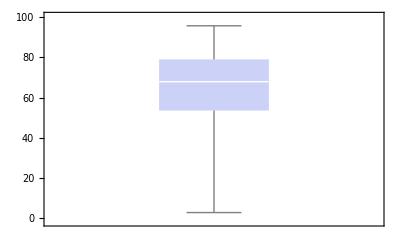
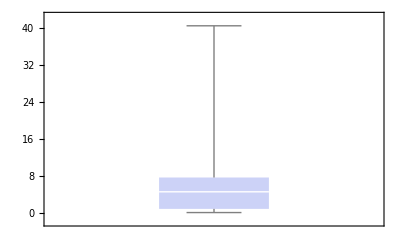
GraphicsGrid[{{-Graphics-hPeriod absolute error E_A [%],-Graphics-hPeriod period corrected error E_P [%]}},Spacings→{Periodogram period estimation errorsTop,Automatic},BaseStyle→FontSize→18]

```mathematica
chart=GraphicsRow[{Labeled[BoxWhiskerChart[hPeriod*100,ImageSize->{400,270}], "hPeriod absolute error E_A [%]"], Labeled[BoxWhiskerChart[hPeriodMultiples*100,ImageSize->{400,270}],"hPeriod period corrected error E_P [%]"]}, BaseStyle->FontSize->18]
```

```mathematica
bigChart=Show[chart,ImageSize->{899,339},AspectRatio->Full]
```

-Graphics-

```mathematica
Export["Skola\\Diplomka\\thesis\\images\\periodogram_errors.pdf",bigChart,"PDF"]
```

Export::noopen: Cannot open "Skola\\Diplomka\\thesis\\images\\periodogram_errors.pdf".

$Failed